```mathematica
Quit[]
```

```mathematica
Question 1) c)
```

```mathematica
A=({{0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 1}, {-1, 0, 1, -1, 0.5, 0.5}, {0, -1, 1, 1, -2, 1}, {2, 1, -3, 1, 1, -2}});B=({{0}, {0}, {0}, {0}, {0}, {1}});Cm=({{1, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0}});Dm=({{0}, {0}, {0}});
x[t_]:={x1[t],x2[t],x3[t], x4[t], x5[t], x6[t]};
y[t_]:=Cm.x[t];
```

```mathematica
n=Dimensions[A][[1]];
r=Dimensions[B][[2]];
m =Dimensions[Cm][[1]];
Print["n = ", n,"\t r = ",r,"\t m = ",m]
P=Join[B,A.B,A.A.B,A.A.A.B,A.A.A.A.B,A.A.A.A.A.B, 2];
Print["P = ",MatrixForm[P]]
Print["Rank of P: ",MatrixRank[P]]
If[MatrixRank[P]==n,Print["System is controllable."],Print["System is uncontrollable."]]
```

n = 6	 r = 1	 m = 3

P = (0 | 0. | 0.5 | 0. | -2.5 | 7.5
0 | 0. | 1. | -2.5 | 4.5 | -6.
0 | 1. | -2. | 2.5 | 0.5 | -9.
0 | 0.5 | 0. | -2.5 | 7.5 | -12.
0 | 1. | -2.5 | 4.5 | -6. | 6.5
1 | -2. | 2.5 | 0.5 | -9. | 17.5)

Rank of P: 6

System is controllable.

```mathematica
Q=Join[Cmᵀ,Aᵀ.Cmᵀ,Aᵀ.Aᵀ.Cmᵀ,Aᵀ.Aᵀ.Aᵀ.Cmᵀ,Aᵀ.Aᵀ.Aᵀ.Aᵀ.Cmᵀ,Aᵀ.Aᵀ.Aᵀ.Aᵀ.Aᵀ.Cmᵀ, 2];
Print["Q = ",MatrixForm[Q]]
Print["rank(Q) = ",MatrixRank[Q]]
If[MatrixRank[Q]==n,Print["System is observable."],Print["System is not observable."]]
```

Q = (1 | 0 | 0 | 0. | 0. | 0. | -1. | 0. | 2. | 2. | 1. | -5. | -1. | -3. | 5. | -5. | 4. | 6.
0 | 1 | 0 | 0. | 0. | 0. | 0. | -1. | 1. | 0. | 3. | -3. | 1. | -7. | 5. | -5. | 14. | -4.
0 | 0 | 1 | 0. | 0. | 0. | 1. | 1. | -3. | -2. | -4. | 8. | 0. | 10. | -10. | 10. | -18. | -2.
0 | 0 | 0 | 1. | 0. | 0. | -1. | 1. | 1. | 1. | -2. | 0. | 0. | 5. | -5. | -1. | -13. | 15.
0 | 0 | 0 | 0. | 1. | 0. | 0.5 | -2. | 1. | -1. | 4.5 | -2.5 | 2.5 | -9.5 | 4.5 | -6.5 | 19. | -6.
0 | 0 | 0 | 0. | 0. | 1. | 0.5 | 1. | -2. | 0. | -2.5 | 2.5 | -2.5 | 4.5 | 0.5 | 7.5 | -6. | -9.)

rank(Q) = 6

System is observable.

```mathematica
Eigenvalues[A]//N //Chop
```

{-2.,-1.2267+1.46771 ⅈ,-1.2267-1.46771 ⅈ,-0.546602,0.+1.01808×10^-8 ⅈ,0.-1.01808×10^-8 ⅈ}

```mathematica
Open loop step response
```

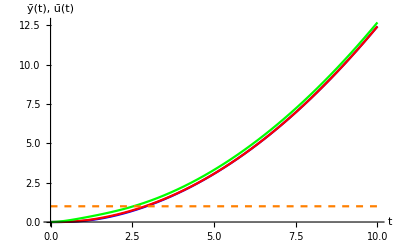

```mathematica
u[t_]={u1[t]};
EqOpenLoop=Thread[x'[t]==A.x[t]+B.u[t]]//Flatten;
IC={x1[0]==0,x2[0]==0,x3[0]==0, x4[0]==0,x5[0]==0, x6[0]==0 };
Inputs={u1[t]->1}; tmax= 10;
OLResponse=NDSolve[{EqOpenLoop/.Inputs,IC},x[t],{t,0,tmax}];
Plot[Evaluate[{y[t]/.OLResponse,u1[t]/.Inputs,u2[t]/.Inputs}],{t,0,tmax}, AxesLabel->{"t","ȳ(t), ū(t)"}, PlotRange->All,PlotStyle->{Blue,Red,Green,{Dashed, Orange},{Dashed, Purple}}]
```

None of the eigenvalues are positive.  
However,I see 2 eigenvalues has  a real part of zero and imaginary value that is  very close to zero (ω =~ 0, 1/s^2 in s-plane, as transfer function).  System is not going to be damped and value will increase without any damping.

```mathematica
Question 2
a)
```

```mathematica
Quit[]
```

```mathematica
A=({{0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1, 0}, {0, 0, -1, 0, 0, 1}, {-1, 0, 1, -1, 1, 4}, {0, -1, 1, 1, -2, 1}, {0, 1, -1, 1, 1, -2}});B=({{0, 1}, {0, 0}, {1, 0}, {0, 0}, {0, 0}, {1, 0}});Cm=({{1, 0, 0, 0, 0, 0}, {0, 1, 0, 0, 0, 0}, {0, 0, 1, 0, 0, 0}, {0, 0, 0, 1, 0, 0}});Dm=({{0, 1}, {0, 0}, {1, 0}, {0, 0}});
x[t_]:={x1[t],x2[t],x3[t], x4[t], x5[t], x6[t]}
y[t_]:=Cm.x[t]
```

```mathematica
Let's check observability, controllability and stability first!
```

```mathematica
n=Dimensions[A][[1]];
r=Dimensions[B][[2]];
m =Dimensions[Cm][[1]];
Print["n = ", n,"\t r = ",r,"\t m = ",m]
P=Join[B,A.B,A.A.B,A.A.A.B,A.A.A.A.B,A.A.A.A.A.B, 2];
Print["P = ",MatrixForm[P]]
Print["Rank of P: ",MatrixRank[P]]
If[MatrixRank[P]==n,Print["System is controllable."],Print["System is uncontrollable."]]
```

n = 6	 r = 2	 m = 4

P = (0 | 1 | 0 | 0 | 5 | -1 | -15 | 1 | 57 | -5 | -181 | 13
0 | 0 | 0 | 0 | 2 | 0 | -2 | -1 | -3 | 2 | 43 | -7
1 | 0 | 0 | 0 | -3 | 0 | 16 | -1 | -54 | 3 | 166 | -10
0 | 0 | 5 | -1 | -15 | 1 | 57 | -5 | -181 | 13 | 561 | -40
0 | 0 | 2 | 0 | -2 | -1 | -3 | 2 | 43 | -7 | -206 | 21
1 | 0 | -3 | 0 | 13 | -1 | -38 | 2 | 112 | -7 | -311 | 19)

Rank of P: 6

System is controllable.

```mathematica
Q=Join[Cmᵀ,Aᵀ.Cmᵀ,Aᵀ.Aᵀ.Cmᵀ,Aᵀ.Aᵀ.Aᵀ.Cmᵀ,Aᵀ.Aᵀ.Aᵀ.Aᵀ.Cmᵀ,Aᵀ.Aᵀ.Aᵀ.Aᵀ.Aᵀ.Cmᵀ, 2];
Print["Q = ",MatrixForm[Q]]
Print["rank(Q) = ",MatrixRank[Q]]
If[MatrixRank[Q]==n,Print["System is observable."],Print["System is not observable."]]
```

Q = (1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 1 | 1 | -1 | -1 | -5 | -5 | 2 | 3 | 13 | 13 | -7 | -10 | -40
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 3 | 3 | 3 | -4 | -11 | -11 | -4 | 14 | 40 | 40 | 0 | -42 | -127
0 | 0 | 1 | 0 | 0 | 0 | -1 | 1 | 1 | 1 | 0 | -5 | -5 | -3 | 5 | 21 | 21 | 5 | -22 | -74 | -74 | 2 | 74 | 241
0 | 0 | 0 | 1 | 1 | 0 | 0 | -1 | -1 | 1 | 1 | 5 | 5 | -2 | -3 | -13 | -13 | 7 | 10 | 40 | 40 | -21 | -29 | -114
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | -2 | 1 | 1 | 1 | 5 | -3 | -4 | -4 | -8 | 10 | 20 | 20 | 11 | -28 | -67
0 | 0 | 0 | 0 | 0 | 0 | 1 | 4 | 4 | 1 | -3 | -10 | -10 | 1 | 11 | 36 | 36 | -8 | -32 | -107 | -107 | 41 | 92 | 320)

rank(Q) = 6

System is observable.

```mathematica
Eigenvalues[A]//N //Chop
```

{-2.74675,-1.93928+0.368654 ⅈ,-1.93928-0.368654 ⅈ,0.950416,-0.515726,0.190612}

```mathematica
Because of the positive eigenvalues, open loop system is not stable!
```

#### Output Controllability matrix :

```mathematica
Po=Join[Cm.B,Cm.A.B,Cm.A.A.B,Cm.A.A.A.B,Cm.A.A.A.A.B,Cm. A.A.A.A.A.B, 2];
Print["P_o = ",MatrixForm[Po]]
Print["Rank of Po: ",MatrixRank[Po]]
If[MatrixRank[Po]==m,Print["System is output controllable."],Print["System is output uncontrollable."]]
```

P_o = (0 | 1 | 0 | 0 | 5 | -1 | -15 | 1 | 57 | -5 | -181 | 13
0 | 0 | 0 | 0 | 2 | 0 | -2 | -1 | -3 | 2 | 43 | -7
1 | 0 | 0 | 0 | -3 | 0 | 16 | -1 | -54 | 3 | 166 | -10
0 | 0 | 5 | -1 | -15 | 1 | 57 | -5 | -181 | 13 | 561 | -40)

Rank of Po: 4

System is output controllable.

#### Desired closed - loop eigenvalues :

```mathematica
{λ1,λ2,λ3, λ4}={-3,-3,-4,-4};
```

#### Form X = [I λ - A ⋮ B] matrix and obtain the null space:

```mathematica
Imat=IdentityMatrix[n];
X=Join[Imat λ-A,B,2]//Simplify; MatrixForm[X]
U=NullSpace[X]ᵀ//Simplify; MatrixForm[U]
```

(λ | 0 | 0 | -1 | 0 | 0 | 0 | 1
0 | λ | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 1+λ | 0 | 0 | -1 | 1 | 0
1 | 0 | -1 | 1+λ | -1 | -4 | 0 | 0
0 | 1 | -1 | -1 | 2+λ | -1 | 0 | 0
0 | -1 | 1 | -1 | -1 | 2+λ | 1 | 0)

((9+21 λ+6 λ^2-9 λ^3-6 λ^4-λ^5)/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6) | -(6+17 λ+15 λ^2+5 λ^3)/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6)
(5+4 λ+λ^2)/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6) | -(3+5 λ+10 λ^2+2 λ^3)/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6)
((1+λ) (2+λ))/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6) | -(2-3 λ^2+7 λ^3+6 λ^4+λ^5)/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6)
((1+λ) (1+5 λ+4 λ^2+λ^3))/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6) | -(λ (6+17 λ+15 λ^2+5 λ^3))/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6)
(λ (5+4 λ+λ^2))/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6) | -(λ (3+5 λ+10 λ^2+2 λ^3))/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6)
((1+λ)^2 (2+λ))/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6) | -(1+5 λ+9 λ^2+5 λ^3+3 λ^4+λ^5)/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6)
0 | 1
1 | 0)

#### Form Ψ and ℱ ' matrices by partitioning U :

```mathematica
Ψ=Take[U,n];MatrixForm[Ψ]
ℱp:=Take[U,-r];MatrixForm[ℱp]
```

((9+21 λ+6 λ^2-9 λ^3-6 λ^4-λ^5)/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6) | -(6+17 λ+15 λ^2+5 λ^3)/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6)
(5+4 λ+λ^2)/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6) | -(3+5 λ+10 λ^2+2 λ^3)/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6)
((1+λ) (2+λ))/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6) | -(2-3 λ^2+7 λ^3+6 λ^4+λ^5)/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6)
((1+λ) (1+5 λ+4 λ^2+λ^3))/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6) | -(λ (6+17 λ+15 λ^2+5 λ^3))/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6)
(λ (5+4 λ+λ^2))/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6) | -(λ (3+5 λ+10 λ^2+2 λ^3))/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6)
((1+λ)^2 (2+λ))/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6) | -(1+5 λ+9 λ^2+5 λ^3+3 λ^4+λ^5)/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6))

(0 | 1
1 | 0)

#### Form composite matrices Ω = [Ψ (λ1) Ψ (λ2) ... Ψ (λn)] , Ω' = C Ω, and Λ' = [ℱ' (λ1) ℱ ' (λ2) ... ℱ '(λn)] :

```mathematica
Ω=Join[Ψ/.λ->λ1,Ψ/.λ->λ2,Ψ/.λ->λ3,Ψ/.λ->λ4,2];
Ωp=Cm.Ω//Simplify;MatrixForm[Ωp]
Λp=Join[ℱp/.λ->λ1,ℱp/.λ->λ2,ℱp/.λ->λ3,ℱp/.λ->λ4,2];MatrixForm[Λp]
```

(0 | 9/2 | 0 | 9/2 | 85/397 | 142/397 | 85/397 | 142/397
1/5 | -12/5 | 1/5 | -12/5 | 5/397 | -15/397 | 5/397 | -15/397
1/5 | -29/10 | 1/5 | -29/10 | 6/397 | -18/397 | 6/397 | -18/397
1 | -27/2 | 1 | -27/2 | 57/397 | -568/397 | 57/397 | -568/397)

(0 | 1 | 0 | 1 | 0 | 1 | 0 | 1
1 | 0 | 1 | 0 | 1 | 0 | 1 | 0)

#### Form the G' and 𝒥 ' matrices by selecting linearly independent columns, one for each eigenvalue, up to m :

```mathematica
ColumnChoice={1,2,5,6};
Gp=Ωp[[All,ColumnChoice]];MatrixForm[Gp]
𝒥p=Λp[[All,ColumnChoice]];MatrixForm[𝒥p]
Det[Gp]//N
```

(0 | 9/2 | 85/397 | 142/397
1/5 | -12/5 | 5/397 | -15/397
1/5 | -29/10 | 6/397 | -18/397
1 | -27/2 | 57/397 | -568/397)

(0 | 1 | 0 | 1
1 | 0 | 1 | 0)

0.0309824

#### Solve for K :

```mathematica
Kstar=𝒥p.Inverse[Gp]//N//Simplify; MatrixForm[Kstar]
```

(0.252033 | 1.22764 | 2.5122 | -0.747967
3.92683 | -8.19512 | 8.56098 | 0.926829)

```mathematica
Eigenvalues[A-B.Kstar.Cm]
```

{-4.,-4.,-3.,-3.,1.06458,0.4964}

As expected,  4 eigenvalues (m = 4) were placed at the desired values . Even if question would ask to place more than 4, output feedback method can only be able to place "m" eigenvalues . 
  
  In summary, output feedback result is not acceptable . We need state feedback method even though it is computationally expensive and requires additional sensors .

```mathematica
Question 2
b)
```

#### Form X = [I λ - A ⋮ B] matrix and obtain the null space:

```mathematica
{λ1,λ2,λ3, λ4, λ5, λ6}={-3,-3, -4,-4,-5,-5};
Imat=IdentityMatrix[n];
```

```mathematica
X=Join[Imat λ-A,B,2]; MatrixForm[X]
U=NullSpace[X]ᵀ//Simplify; MatrixForm[U]
```

(λ | 0 | 0 | -1 | 0 | 0 | 0 | 1
0 | λ | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 1+λ | 0 | 0 | -1 | 1 | 0
1 | 0 | -1 | 1+λ | -1 | -4 | 0 | 0
0 | 1 | -1 | -1 | 2+λ | -1 | 0 | 0
0 | -1 | 1 | -1 | -1 | 2+λ | 1 | 0)

((9+21 λ+6 λ^2-9 λ^3-6 λ^4-λ^5)/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6) | -(6+17 λ+15 λ^2+5 λ^3)/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6)
(5+4 λ+λ^2)/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6) | -(3+5 λ+10 λ^2+2 λ^3)/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6)
((1+λ) (2+λ))/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6) | -(2-3 λ^2+7 λ^3+6 λ^4+λ^5)/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6)
((1+λ) (1+5 λ+4 λ^2+λ^3))/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6) | -(λ (6+17 λ+15 λ^2+5 λ^3))/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6)
(λ (5+4 λ+λ^2))/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6) | -(λ (3+5 λ+10 λ^2+2 λ^3))/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6)
((1+λ)^2 (2+λ))/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6) | -(1+5 λ+9 λ^2+5 λ^3+3 λ^4+λ^5)/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6)
0 | 1
1 | 0)

#### Form Ψ and ℱ matrices by partitioning U :

```mathematica
Ψ=Take[U,n];MatrixForm[Ψ]
ℱ:=Take[U,-r];MatrixForm[ℱ]
```

((9+21 λ+6 λ^2-9 λ^3-6 λ^4-λ^5)/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6) | -(6+17 λ+15 λ^2+5 λ^3)/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6)
(5+4 λ+λ^2)/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6) | -(3+5 λ+10 λ^2+2 λ^3)/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6)
((1+λ) (2+λ))/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6) | -(2-3 λ^2+7 λ^3+6 λ^4+λ^5)/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6)
((1+λ) (1+5 λ+4 λ^2+λ^3))/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6) | -(λ (6+17 λ+15 λ^2+5 λ^3))/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6)
(λ (5+4 λ+λ^2))/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6) | -(λ (3+5 λ+10 λ^2+2 λ^3))/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6)
((1+λ)^2 (2+λ))/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6) | -(1+5 λ+9 λ^2+5 λ^3+3 λ^4+λ^5)/(1-3 λ-12 λ^2-λ^3+10 λ^4+6 λ^5+λ^6))

(0 | 1
1 | 0)

#### Form composite matrices Ω = [Ψ (λ1) Ψ (λ2) ... Ψ (λn)] and Λ = [ℱ (λ1) ℱ (λ2) ... ℱ (λn)] :

```mathematica
Ω=Join[Ψ/.λ->λ1,Ψ/.λ->λ2,Ψ/.λ->λ3,Ψ/.λ->λ4,Ψ/.λ->λ5,Ψ/.λ->λ6, 2]//Simplify;MatrixForm[Ω]
Λ=Join[ℱ/.λ->λ1,ℱ/.λ->λ2,ℱ/.λ->λ3,ℱ/.λ->λ4,ℱ/.λ->λ5,ℱ/.λ->λ6, 2];MatrixForm[Λ]
```

(0 | 9/2 | 0 | 9/2 | 85/397 | 142/397 | 85/397 | 142/397 | 277/1483 | 329/2966 | 277/1483 | 329/2966
1/5 | -12/5 | 1/5 | -12/5 | 5/397 | -15/397 | 5/397 | -15/397 | 5/1483 | 11/1483 | 5/1483 | 11/1483
1/5 | -29/10 | 1/5 | -29/10 | 6/397 | -18/397 | 6/397 | -18/397 | 6/1483 | 323/2966 | 6/1483 | 323/2966
1 | -27/2 | 1 | -27/2 | 57/397 | -568/397 | 57/397 | -568/397 | 98/1483 | -1645/2966 | 98/1483 | -1645/2966
-3/5 | 36/5 | -3/5 | 36/5 | -20/397 | 60/397 | -20/397 | 60/397 | -25/1483 | -55/1483 | -25/1483 | -55/1483
-2/5 | 34/5 | -2/5 | 34/5 | -18/397 | 451/397 | -18/397 | 451/397 | -24/1483 | 837/1483 | -24/1483 | 837/1483)

(0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1
1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0)

#### Form the G and 𝒥 matrices by selecting linearly independent columns, one for each eigenvalue :

```mathematica
ColumnChoice={1,2,6,7,9,12};
G=Ω[[All,ColumnChoice]];MatrixForm[G]
𝒥=Λ[[All,ColumnChoice]];MatrixForm[𝒥]
Det[G]//N
```

(0 | 9/2 | 142/397 | 85/397 | 277/1483 | 329/2966
1/5 | -12/5 | -15/397 | 5/397 | 5/1483 | 11/1483
1/5 | -29/10 | -18/397 | 6/397 | 6/1483 | 323/2966
1 | -27/2 | -568/397 | 57/397 | 98/1483 | -1645/2966
-3/5 | 36/5 | 60/397 | -20/397 | -25/1483 | -55/1483
-2/5 | 34/5 | 451/397 | -18/397 | -24/1483 | 837/1483)

(0 | 1 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 1 | 0)

-3.39702×10^-6

#### Solve for K :

```mathematica
Ksf=𝒥.Inverse[G]//N;MatrixForm[Ksf]
```

(-0.5 | 25.5 | 4.5 | 5. | 14. | 6.5
7. | 136.4 | 22.6 | -0.4 | 53.6 | -4.4)

#### Test close loop eigenvalues :

```mathematica
Eigenvalues[A-B.Ksf]
```

{-5.,-5.,-4.,-4.,-3.,-3.}

## All eigenvalues are at desired position!

Question 2 
 c)

#### Partition the system into m measurable states and n - m states that need to be estimated :

```mathematica
Print["x = ", MatrixForm[x[t]]]
xv1[t_]:=Take[x[t],m];
xv2[t_]:=Take[x[t],-(n-m)];
Print["x_v1 = ", MatrixForm[xv1[t]],"\t x_v2 = ", MatrixForm[xv2[t]]]
Print["A = ",MatrixForm[A]]
A11=Take[A,m,m]; 
A12=Take[A,m,{m+1,n}];
A21=Take[A,{m+1,n},m];
A22=Take[A,{m+1,n},{m+1,n}];
Print["A11 = ",MatrixForm[A11], "\t A12 = ",MatrixForm[A12],"\t A21 = ",MatrixForm[A21], "\t A22 = ",MatrixForm[A22]]
B1=Take[B,m];
B2=Take[B,-(n-m)];
Print["B = ",MatrixForm[B]]
Print["B_1 = ",MatrixForm[B1], "\t B_2 = ",MatrixForm[B2]]
```

x = (x1[t]
x2[t]
x3[t]
x4[t]
x5[t]
x6[t])

x_v1 = (x1[t]
x2[t]
x3[t]
x4[t])	 x_v2 = (x5[t]
x6[t])

A = (0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | -1 | 0 | 0 | 1
-1 | 0 | 1 | -1 | 1 | 4
0 | -1 | 1 | 1 | -2 | 1
0 | 1 | -1 | 1 | 1 | -2)

A11 = (0 | 0 | 0 | 1
0 | 0 | 0 | 0
0 | 0 | -1 | 0
-1 | 0 | 1 | -1)	 A12 = (0 | 0
1 | 0
0 | 1
1 | 4)	 A21 = (0 | -1 | 1 | 1
0 | 1 | -1 | 1)	 A22 = (-2 | 1
1 | -2)

B = (0 | 1
0 | 0
1 | 0
0 | 0
0 | 0
1 | 0)

B_1 = (0 | 1
0 | 0
1 | 0
0 | 0)	 B_2 = (0 | 0
1 | 0)

#### Form Xo = [I λ - A_22ᵀ ⋮ A_12ᵀ] matrix and obtain the null space:

```mathematica
{λr1,λr2 }={-10, -12}; 
Ir=IdentityMatrix[n-m];
Xr=Join[Ir λ-A22ᵀ,A12ᵀ,2];MatrixForm[Xr];
Ur = NullSpace[Xr]ᵀ//Simplify;
MatrixForm[Ur];
Ψr=Take[Ur,n-m];MatrixForm[Ψr];
ℱr:=Take[Ur,-m];MatrixForm[ℱr];
Ωr=Join[Ψr/.λ->λr1,Ψr/.λ->λr2,2];Print["Ωr =", MatrixForm[Ωr]]
Λr=Join[ℱr/.λ->λr1,ℱr/.λ->λr2,2];Print["Λr =", MatrixForm[Λr]]
```

Ωr =(4/63 | -1/63 | 8/63 | 0 | 2/33 | -1/99 | 10/99 | 0
31/63 | 8/63 | -1/63 | 0 | 13/33 | 10/99 | -1/99 | 0)

Λr =(0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 1 | 0 | 0 | 0)

#### Form the G and 𝒥 matrices by selecting linearly independent columns, one for each eigenvalue :

```mathematica
ColumnChoice={2, 5};
Gr=Ωr[[All,ColumnChoice]];MatrixForm[Gr]
𝒥r=Λr[[All,ColumnChoice]];MatrixForm[𝒥r]
Det[Gr]//N
```

(-1/63 | 2/33
8/63 | 13/33)

(0 | 0
0 | 0
1 | 0
0 | 1)

-0.013949

#### Solve for Lr :

```mathematica
Lr=Transpose[𝒥r.Inverse[Gr]];
MatrixForm[Lr]
```

(0 | 0 | -819/29 | 264/29
0 | 0 | 126/29 | 33/29)

#### Reduced Order Observer Matrix:

```mathematica
Clear[u];
Ar=A22-Lr.A12; MatrixForm[Ar]
```

(-322/29 | -208/29
-4/29 | -316/29)

#### Test reduced order observer eigenvalues :

```mathematica
Eigenvalues[Ar]
```

{-12,-10}

## All eigenvalues are at desired position!

## Question 2 d)

State  Feedback + Observer simulation

## d) Reduced Order Observer Feedback Simulation:

```mathematica
Clear[u,v,v1,v2]
v[t_]:={v1[t],v2[t]};
xro[t_]={xro4[t],xro5[t]}
Imr=IdentityMatrix[r];
(*F=Imr*)
Cr=Take[Cm,r];(* required if m>r*)
F=Inverse[−Cr.Inverse[A−B.Ksf].B]
xhat[t]={xv1[t],xro[t]}//Flatten
u[t_]:=F.v[t]-Ksf.xhat[t]
MatrixForm[u[t]]
yr[t_]:= xv1'[t]-A11.xv1[t]-B1.u[t]
MatrixForm[yr[t]]
zr[t_]:=A21.xv1[t]+B2.u[t] 
MatrixForm[zr[t]]
```

{xro4[t],xro5[t]}

{{-1.69177×10^-16,30.},{40.,84.}}

{x1[t],x2[t],x3[t],x4[t],xro4[t],xro5[t]}

(-1.69177×10^-16 v1[t]+30. v2[t]+0.5 x1[t]-25.5 x2[t]-4.5 x3[t]-5. x4[t]-14. xro4[t]-6.5 xro5[t]
40. v1[t]+84. v2[t]-7. x1[t]-136.4 x2[t]-22.6 x3[t]+0.4 x4[t]-53.6 xro4[t]+4.4 xro5[t])

(-40. v1[t]-84. v2[t]+7. x1[t]+136.4 x2[t]+22.6 x3[t]-1.4 x4[t]+53.6 xro4[t]-4.4 xro5[t]+x1'[t]
x2'[t]
1.69177×10^-16 v1[t]-30. v2[t]-0.5 x1[t]+25.5 x2[t]+5.5 x3[t]+5. x4[t]+14. xro4[t]+6.5 xro5[t]+x3'[t]
x1[t]-x3[t]+x4[t]+x4'[t])

(-x2[t]+x3[t]+x4[t]
-1.69177×10^-16 v1[t]+30. v2[t]+0.5 x1[t]-24.5 x2[t]-5.5 x3[t]-4. x4[t]-14. xro4[t]-6.5 xro5[t])

```mathematica
EqRedObsFdbk=Thread[x'[t]==A.x[t]-B.Ksf.xhat[t]+B.F.v[t]//Chop];
EqRedObserver=Thread[xro'[t]==Ar.xro[t]+Lr.yr[t]+zr[t]//Chop];
ICro={xro4[0]==-3,xro5[0]==-1}; 
y[t_]:=Cm.x[t]      
TableForm[{EqRedObsFdbk,EqRedObserver}//Flatten]
```

x1'[t]==40. v1[t]+84. v2[t]-7. x1[t]-136.4 x2[t]-22.6 x3[t]+1.4 x4[t]-53.6 xro4[t]+4.4 xro5[t]
x2'[t]==x5[t]
x3'[t]==30. v2[t]+0.5 x1[t]-25.5 x2[t]-5.5 x3[t]-5. x4[t]+x6[t]-14. xro4[t]-6.5 xro5[t]
x4'[t]==-x1[t]+x3[t]-x4[t]+x5[t]+4 x6[t]
x5'[t]==-x2[t]+x3[t]+x4[t]-2 x5[t]+x6[t]
x6'[t]==30. v2[t]+0.5 x1[t]-24.5 x2[t]-5.5 x3[t]-4. x4[t]+x5[t]-2 x6[t]-14. xro4[t]-6.5 xro5[t]
xro4'[t]==-x2[t]+x3[t]+x4[t]-(322 xro4[t])/29-(208 xro5[t])/29-819/29 (-30. v2[t]-0.5 x1[t]+25.5 x2[t]+5.5 x3[t]+5. x4[t]+14. xro4[t]+6.5 xro5[t]+x3'[t])+264/29 (x1[t]-x3[t]+x4[t]+x4'[t])
xro5'[t]==30. v2[t]+0.5 x1[t]-24.5 x2[t]-5.5 x3[t]-4. x4[t]-14.1379 xro4[t]-17.3966 xro5[t]+126/29 (-30. v2[t]-0.5 x1[t]+25.5 x2[t]+5.5 x3[t]+5. x4[t]+14. xro4[t]+6.5 xro5[t]+x3'[t])+33/29 (x1[t]-x3[t]+x4[t]+x4'[t])

```mathematica
yd[t_]:={y1d[t],y2d[t],y3d[t], y4d[t]};
DesOut={y1d[t]-> 1,y2d[t]-> 1,y3d[t]-> 1, y4d[t]-> 1}
tmax=5;
IC2={x1[0]==-1,x2[0]==1,x3[0]==-3, x4[0]==3,x5[0]==5, x6[0]==-3}
DesInput={v1[t]->1, v2[t]->1};
RedObsFdbkResponse=NDSolve[{EqRedObsFdbk/.DesInput, IC2 ,EqRedObserver/.DesInput,ICro},{x[t],xro4[t],xro5[t]}//Flatten,{t,0,tmax}];
```

{y1d[t]→1,y2d[t]→1,y3d[t]→1,y4d[t]→1}

{x1[0]==-1,x2[0]==1,x3[0]==-3,x4[0]==3,x5[0]==5,x6[0]==-3}

Checking if NDSolve worked

```mathematica
RedObsFdbkResponse
```

{{x1[t]→InterpolatingFunction[…][t],x2[t]→InterpolatingFunction[…][t],x3[t]→InterpolatingFunction[…][t],x4[t]→InterpolatingFunction[…][t],x5[t]→InterpolatingFunction[…][t],x6[t]→InterpolatingFunction[…][t],xro4[t]→InterpolatingFunction[…][t],xro5[t]→InterpolatingFunction[…][t]}}

Estimated States x5 and x6 (named xro4, and xro5 to not change the code)

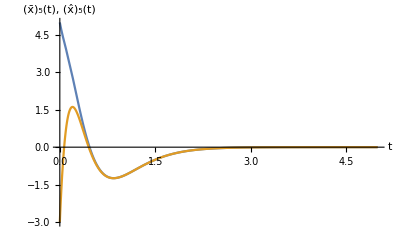

```mathematica
Plot[Evaluate[{x5[t],xro4[t]}/.RedObsFdbkResponse],{t,0,tmax}, AxesLabel->{"t","(x̄)_5(t), (x̂)_5(t)"}, PlotRange->All]
```

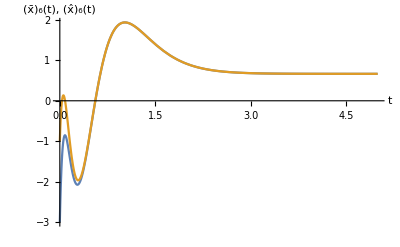

```mathematica
Plot[Evaluate[{x6[t],xro5[t]}/.RedObsFdbkResponse],{t,0,tmax}, AxesLabel->{"t","(x̄)_6(t), (x̂)_6(t)"}, PlotRange->All]
```

Even though initial guess is incorrect, estimation error yields to zero in time .

Let’s see the output states:

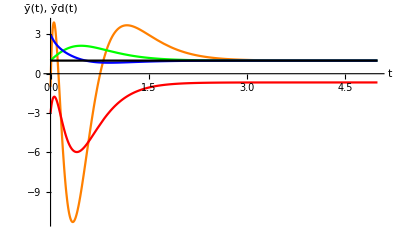

```mathematica
Plot[Evaluate[{y[t]/.RedObsFdbkResponse,y1d[t]/.DesOut}],{t,0,tmax}, AxesLabel->{"t","ȳ(t), ȳd(t)"}, PlotRange->All,PlotStyle->{Orange,Green,Red,Blue ,Black}]
```

Except for one output, it is possible to reach desired output .

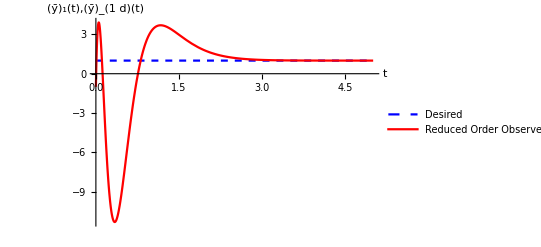

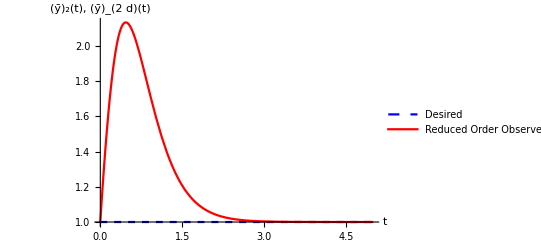

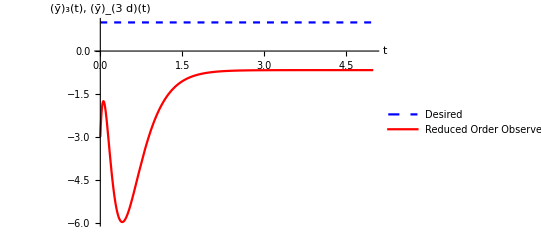

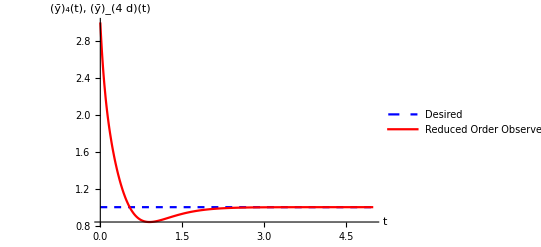

```mathematica
legend={"Desired","Reduced Order Observer"};
style={{Dashed, Blue},Red} ;
Plot[{y1d[t]/.DesOut,Evaluate[y[t][[1]]/.RedObsFdbkResponse]},{t,0,tmax}, AxesLabel->{"t","(ȳ)_1(t),(ȳ)_(1  d)(t)"}, PlotRange->All,PlotStyle->style ,PlotLegends->legend]
Plot[{y2d[t]/.DesOut,Evaluate[y[t][[2]]/.RedObsFdbkResponse]},{t,0,tmax}, AxesLabel->{"t","(ȳ)_2(t), (ȳ)_(2  d)(t)"}, PlotRange->All,PlotStyle->style ,PlotLegends->legend]
Plot[{y3d[t]/.DesOut,Evaluate[y[t][[3]]/.RedObsFdbkResponse]},{t,0,tmax}, AxesLabel->{"t","(ȳ)_3(t), (ȳ)_(3  d)(t)"}, PlotRange->All,PlotStyle->style ,PlotLegends->legend]

Plot[{y4d[t]/.DesOut,Evaluate[y[t][[4]]/.RedObsFdbkResponse]},{t,0,tmax}, AxesLabel->{"t","(ȳ)_4(t), (ȳ)_(4  d)(t)"}, PlotRange->All,PlotStyle->style ,PlotLegends->legend]
```

#### Same with the previous plot but one by one. Steady state error is zero except for 1 output . Output state 3 has - 2 steady state error . Controller - Observer shows transient response . This can be reduced with an optimal controller in which gain change over time .